## Visual Equation Constrained Optimization in 2D

Written by Adam B. Levy, Semptember 2011

This notebook gives a template for visually observing the progress of different numerical methods for optimizing a function f(x,y) of two-variables subject to a constraint g(x,y) = 0.

## Initializing the Guess and Objective

```mathematica
Off[General::spell]
Off[General::spell1]
Clear[f]
nb=SelectedNotebook[ ];
inx=2.;
iny=1.;
inlam=1.;
fi=x^2-2 x y+2y^2;
gi=y-(x-y)^2-1;
(*The next commands build partial derivatives that can be used in the iteration function (and an exact line search) while accepting current guesses in the argument later*)
fy[x_,y_]=D[f[x,y],y];
fx[x_,y_]=D[f[x,y],x];
fxx[x_,y_]=D[fx[x,y],x];
fxy[x_,y_]=D[fx[x,y],y];
fyx[x_,y_]=D[fy[x,y],x];
fyy[x_,y_]=D[fy[x,y],y];
PasteButton[Defer[fx[x,y]]];
PasteButton[Defer[fy[x,y]]];
PasteButton[Defer[fxx[x,y]]];
PasteButton[Defer[fxy[x,y]]];
PasteButton[Defer[fyx[x,y]]];
PasteButton[Defer[fyy[x,y]]];
gy[x_,y_]=D[g[x,y],y];
gx[x_,y_]=D[g[x,y],x];
gxx[x_,y_]=D[gx[x,y],x];
gxy[x_,y_]=D[gx[x,y],y];
gyx[x_,y_]=D[gy[x,y],x];
gyy[x_,y_]=D[gy[x,y],y];
PasteButton[Defer[gx[x,y]]];
PasteButton[Defer[gy[x,y]]];
PasteButton[Defer[gxx[x,y]]];
PasteButton[Defer[gxy[x,y]]];
PasteButton[Defer[gyx[x,y]]];
PasteButton[Defer[gyy[x,y]]];

(*The next command iterates the iteration function once and updates the list of guesses*)
IterateOpt[{xo_,yo_,lo_}]:=Module[{xn,yn,ln},{xn,yn,ln}=Evaluate[G[xo,yo,lo]];guessplus=AppendTo[guessplus,N[{xn,yn,ln}]];guess=AppendTo[guess,N[{xn,yn}]];]
(*The next command draws the contour plot of the objective with the guesslist and constraint curve--if there is one--overlayed*)
VisualOpt[list_,f_,g_]:=Module[{xmax,xmin,ymax,ymin},xmax=Max[list[[All,1]]];xmin=Min[list[[All,1]]];ymax=Max[list[[All,2]]];ymin=Min[list[[All,2]]];
Grid[{{Grid[{{"newest 20 guesses"},{If[Length[list]≤19,TableForm[list],TableForm[Take[list,-20]]]}},Alignment->{Center,Center}],Show[ContourPlot[f,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->20,PlotPoints->25],Graphics[{Blue,Line[list]}],Graphics[{Blue,PointSize[Medium],Point[list]}],Graphics[{Blue,PointSize[Large],Point[First[list]]}],Graphics[{Red,PointSize[Large],Point[Last[list]]}],ContourPlot[g,{x,xmin-If[xmax==xmin,1,(xmax-xmin)]/10,xmax+If[xmax==xmin,1,(xmax-xmin)]/10},{y,ymin-If[ymax==ymin,1,(ymax-ymin)]/10,ymax+If[ymax==ymin,1,(ymax-ymin)]/10},Contours->{0},PlotPoints->25,ContourShading->False,ContourStyle->{Thick,Blue}],Frame->True,FrameLabel->{Style["Newest guess is "Style[Last[list],Red],Medium],,Style["First guess is "Style[First[list],Blue],Medium]},ImageSize->Medium]}},ItemSize->{{15,30}},Alignment->{Center,Top},Frame->All]]
(*The next command makes a pop-up box to intiialize the method*)
Start:=Module[{},DialogInput[{Grid[{{TextCell["First Guess"]},{Grid[{{TextCell["x ="],InputField[Dynamic[inx],Number,ImageSize->30],TextCell["y ="],InputField[Dynamic[iny],Number,ImageSize->30],TextCell["λ ="],InputField[Dynamic[inlam],Number,ImageSize->30]}}]}}],Grid[{{TextCell["Objective function"]},{TextCell["f[x,y]"],InputField[Dynamic[fi]]}}],Grid[{{TextCell["Constraint function"]},{TextCell["g[x,y]"],InputField[Dynamic[gi]],TextCell["= 0"]}}],
DefaultButton["Done",DialogReturn[guessplus={{inx,iny,inlam}};guess={{inx,iny}};f[x_,y_]=fi;g[x_,y_]=gi;]]}]]
```

To start the numerical method at a particular guess with a particular objective function, click your cursor after the following "Initialize" command, hit the ENTER button on your keyboard (not the carriage return button), click "Yes" to the initialization question, fill in the appropriate boxes that pop up, and click "Done".

```mathematica
Start
```

## Building the Method

### Iteration Function

The numerical method is determined by an iteration function G(x,y) giving the right side of the update formula for new guesses in terms of old:

(x_new
y_new
λ_new)= G(x_old,y_old,λ_old)

For example, simply assigning the old variables as new would involve the iteration function

G(x,y,λ)={x,y,λ}

since Mathematica represents column vectors as lists {x,y,λ}.

ENTER your iteration function after filling in the □ below using the following pasting buttons

```mathematica
{{fx[x,y], fy[x,y], fxx[x,y], fxy[x,y], fyx[x,y], fyy[x,y]}}
{{gx[x,y], gy[x,y], gxx[x,y], gxy[x,y], gyx[x,y], gyy[x,y]}}
```

```mathematica
G[x_,y_,λ_]:={x,y,λ}-Inverse[{{fxx[x,y]-λ gxx[x,y],fxy[x,y]-λ gxy[x,y],-gx[x,y]},{fyx[x,y]-λ gyx[x,y],fyy[x,y]-λ gyy[x,y],-gy[x,y]},{-gx[x,y],-gy[x,y],0}}].{fx[x,y]-λ gx[x,y],fy[x,y]-λ gy[x,y],-g[x,y]}
```

## Computing Guesses

ENTER the command below to update the new guess from the old.  Repeat as often as you like.

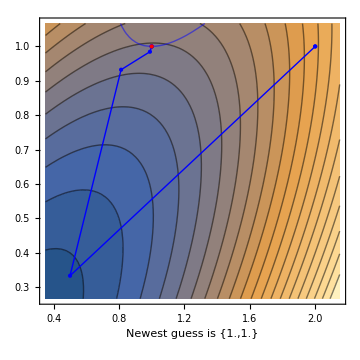
newest 20 guesses
2. | 1.
0.5 | 0.333333
0.8125 | 0.932292
0.988977 | 0.984602
0.999935 | 0.99998
1. | 1.
1. | 1. | -Graphics-

```mathematica
IterateOpt[Last[guessplus]];Print[VisualOpt[guess,fi,gi]]
```

#### Open this cell for details on how to extract old guesses from the full list

If at any time, you need to compute something else involving the guesses, you can extract them from the list guess in which they are stored.  For example, the x and y coordinates respectively of the newest guess are obtained by entering

```mathematica
Last[guess][[1]]
Last[guess][[2]]
```

The function Last retrieves the last element of the list (of pairs), and the [[1]] or [[2]] identifies the first or second component of the pair.

### Make a list of the differences between the guesses and the final guess (our surrogate for the target)

```mathematica
diff=guess-Table[Last[guess],{Length[guess]}]
```

{{1.,0.},{-0.5,-0.666667},{-0.1875,-0.0677083},{-0.0110232,-0.0153982},{-0.0000648574,-0.0000195374},{-1.46372×10^-9,-2.05396×10^-9},{0.,0.}}

### Make a list of errors

```mathematica
erlist=Map[Norm,diff];
TableForm[erlist]
```

1.
0.833333
0.199351
0.0189372
0.0000677362
2.52215×10^-9
0.

### Make a list of new errors divided by old errors

```mathematica
lin={erlist[[2]]/erlist[[1]]};
Do[lin=Append[lin,erlist[[k+1]]/erlist[[k]]],{k,2,Length[erlist]-2}]
TableForm[lin]
```

0.833333
0.239221
0.0949943
0.00357689
0.0000372348

SUPERLINEAR ORDER OF CONVERGENCE, so try for more

### Make a list of new errors divided by old errors-squared

```mathematica
esqlist=erlist^2;
quad={erlist[[2]]/esqlist[[1]]};
Do[quad=Append[quad,erlist[[k+1]]/esqlist[[k]]],{k,2,Length[erlist]-2}]
TableForm[quad]
```

0.833333
0.287065
0.476519
0.188882
0.549703

QUADRATIC ORDER OF CONVERGENCE with constant ~ 0.55

### Make a list of new errors divided by old errors-cubed

```mathematica
ecublist=erlist^3;
cubic={erlist[[2]]/ecublist[[1]]};
Do[cubic=Append[cubic,erlist[[k+1]]/ecublist[[k]]],{k,2,Length[erlist]-2}]
TableForm[cubic]
```

0.833333
0.344478
2.39035
9.97415
8115.35

NOT CUBIC ORDER OF CONVERGENCE.....so quadratic is the best we can get.

### A single table with all the quotients

```mathematica
TableForm[Transpose[{Prepend[lin,"linear error quotients"],Prepend[quad,"quadratic error quotients"],Prepend[cubic,"cubic error quotients"]}]]
```

linear error quotients | quadratic error quotients | cubic error quotients
0.833333 | 0.833333 | 0.833333
0.239221 | 0.287065 | 0.344478
0.0949943 | 0.476519 | 2.39035
0.00357689 | 0.188882 | 9.97415
0.0000372348 | 0.549703 | 8115.35